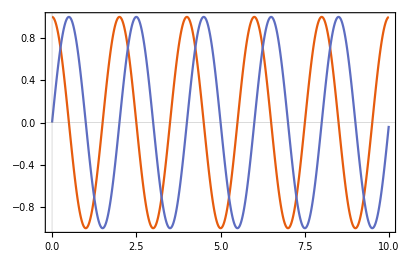

```mathematica
ClearAll["Global`*"];
result=Transpose@Import[FileNameJoin[{NotebookDirectory[],"example1_dataOrg.dat"}]];
time=result[[1]];
ListPlot[Table[Transpose@{time,result[[i]]},{i,2,Length@result}],
Joined->True,
PlotTheme->"Scientific"]
```

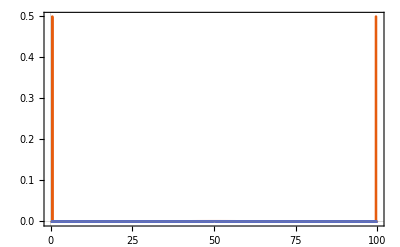

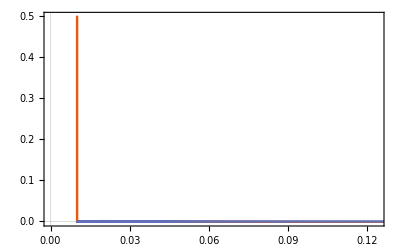

```mathematica
dataRe=Transpose@Import[FileNameJoin[{NotebookDirectory[],"example1_dataDFT_Re.dat"}]];
freq=dataRe[[1]];

ListStepPlot[Table[Transpose[{freq[[2;;]],dataRe[[i]][[2;;]]}],{i,2,Length@dataRe}],
Filling->Axis,
PlotRange->{Automatic,All},
PlotTheme->"Scientific"]

ListStepPlot[Table[Transpose[{1/freq[[2;;]],dataRe[[i]][[2;;]]}],{i,2,Length@dataRe}],
Filling->Axis,
PlotRange->{Automatic,All},
PlotTheme->"Scientific"
]
```

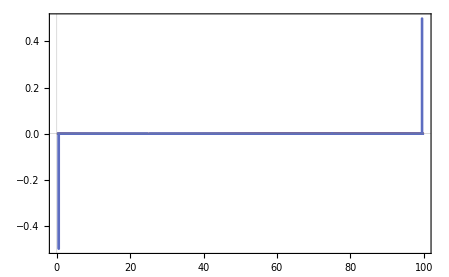

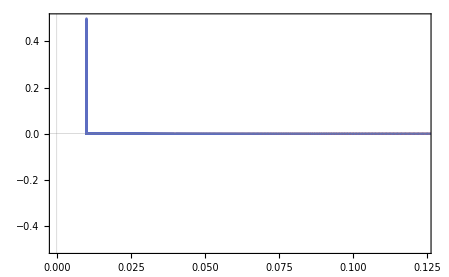

```mathematica
dataIm=Transpose@Import[FileNameJoin[{NotebookDirectory[],"example1_dataDFT_Im.dat"}]];
freq=dataIm[[1]];

ListStepPlot[Table[Transpose[{freq[[2;;]],dataIm[[i]][[2;;]]}],{i,2,Length@dataIm}],
Filling->Axis,
PlotRange->{Automatic,All},
PlotTheme->"Scientific"]

ListStepPlot[Table[Transpose[{1/freq[[2;;]],dataIm[[i]][[2;;]]}],{i,2,Length@dataIm}],
Filling->Axis,
PlotRange->{Automatic,All},
PlotTheme->"Scientific"
]
```